## Explicitly defining an apple

#### Cross section in xz plane

√(1-(Abs[x]-0.3)^2)

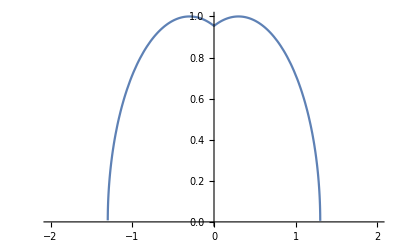

```mathematica
funcx = Sqrt[1-(Abs[x]-.3)^2]
Plot[funcx, {x,-2,2}]
```

### Cross section in yz plane

```mathematica
funcy = Sqrt[1-(Abs[y]-.3)^2]
```

√(1-(-0.3+Abs[y])^2)

### Swept surface

```mathematica
range = x /. Solve[funcx==0,x][[2]]
funcSwept = funcx*funcy
Plot3D[funcSwept,{x,-range,range},{y,-range,range}, AspectRatio->1]
```

1.3

√(1-(-0.3+Abs[x])^2) √(1-(-0.3+Abs[y])^2)

-Graphics3D-

## Explicitly defining a soda can

(2 x^20)/3486784401

(2 x^20)/3486784401

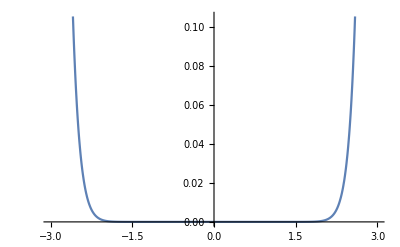

```mathematica
eqn = 2*(x/3)^20
TraditionalForm[eqn]
Plot[eqn, {x,-3,3}]
```

## Defining a lofted surface

### Explicitly

```mathematica
f1=√(1-x^2)
f2=1.4 √(1-x^2)
```

√(1-x^2)

1.4 √(1-x^2)

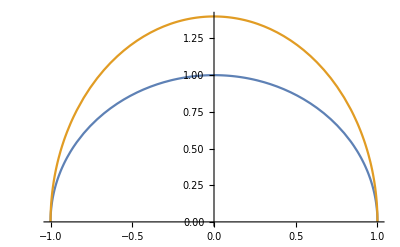

```mathematica
Plot[{f1,f2},{x,-1,1}]
```

```mathematica
Plot3D[(1-z)f1+z f2, {x,-1,1},{z,-1,1},AspectRatio->1]
```

-Graphics3D-

### Implicitly

```mathematica
f1(x_,y_):=x^2+(y+0.4)^2-0.4
f2(x_,y_):=x^2+0.6 y^2-1.3
```

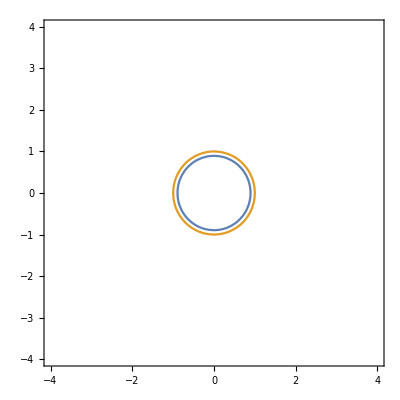

```mathematica
ContourPlot[{f1[x,y]==0,f2[x,y]==0},{x,-4,4},{y,-4,4}]
```

```mathematica
f3(x_,y_,z_):=(1-z) f1(x,y)+z f2(x,y)
```

```mathematica
ContourPlot3D[f3(x,y,z)==0,{x,-1.6,1.6},{y,-1.6,1.6},{z,0,1}]
```

-Graphics3D-